# Implementing REigs from Jia et al

## Script

Pseudocode is on p11 of https://arxiv.org/ftp/arxiv/papers/2102/2102.09693.pdf
There are some typos.  I am doing this in a script first. IRA p10 and IRRA p11

```mathematica
m=23;
d=RandomReal[{1,10},m];
od=0.1 RandomReal[{-1,1},m-1];
B= SparseArray[{
Band[{1,2}]->od,
Band[{2,1}]->od,
Band[{1,1}]->d},{m,m}];
(*B=IdentityMatrix[m];*)
A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
(* Step 1 build v *)
v=RandomReal[{-1,1},m];
v=v/(√(v.B.v));
v0=v;
(* Step 2 and 3 Arnoldi *)
{k,p}={4,3};
k+p+1 ≤ m;
V=ConstantArray[0,{m,k+p+1}];
HBig=ConstantArray[0,{k+p+1,k+p}];
V⟦All,1⟧=v;
Do[
v=LinearSolve[B,A.v];
Do[
HBig⟦j,n⟧=V⟦All,j⟧.B.v;
v=v-HBig⟦j,n⟧ V⟦All,j⟧,
{j,1,n}];
HBig⟦n+1,n⟧=√(v.B.v);
v=v/HBig⟦n+1,n⟧;
V⟦All,n+1⟧=v,
{n,1,k+p}];
MatrixPlot[HBig,PlotLabel->Map[Norm,
{Vᵀ.B.V-IdentityMatrix[k+p+1],
A.V⟦All,1;;k+p⟧-B.V.HBig}]]
```

```mathematica
(* Compute and sort the eigenvalues of the inner matrix *)
H=HBig⟦1;;k+p⟧;
(* define an r *)
λs=Eigenvalues[H]
λs=Sort[Eigenvalues[H]]
σs=λs⟦1;;p⟧;
(*{λs,Qs}=Sort[Eigensystem[Chop[H⟦1;;k+p⟧]]ᵀ]ᵀ; *)
Id=IdentityMatrix[k+p];
Q=Id;
Do[
{Qj,Rj}=QRDecomposition[H-σs⟦j⟧ Id];Qj=Qjᵀ;
H=ConjugateTranspose[Qj].H.Qj;
Q=Q.Qj,
{j,1,p}]
(* Throw away stuff from V and H *)
H=H⟦1;;k,1;;k⟧;
V =V⟦All,1;;k+p⟧.Q⟦All,1;;k⟧;
(* *)
```

## Code

### Initialization

I am returning the HBig matrix the top bit is H.

```mathematica
ArnoldiInitialize[A_,B_,v0_,k_]:=Module[
{m=Length[A],v=v0/(√(v0.B.v0)),HBig,V},
(* Step 2 and 3 Arnoldi *)
V=ConstantArray[0,{m,k+1}];
HBig=ConstantArray[0,{k+1,k}];
V⟦All,1⟧=v;
Do[
v=LinearSolve[B,A.v];
Do[
HBig⟦j,n⟧=V⟦All,j⟧.B.v;
v=v-HBig⟦j,n⟧ V⟦All,j⟧,
{j,1,n}];
HBig⟦n+1,n⟧=√(v.B.v);
v=v/HBig⟦n+1,n⟧;
V⟦All,n+1⟧=v,
{n,1,k}];
{V,Chop[HBig]}
]
```

Testing

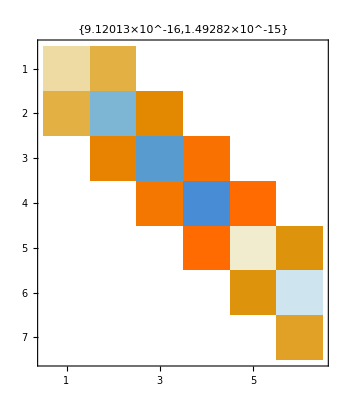

```mathematica
{m,k}={23,6};
d=RandomReal[{1,10},m];od=0.1 RandomReal[{-1,1},m-1];
B= SparseArray[{Band[{1,2}]->od,Band[{2,1}]->od,Band[{1,1}]->d},{m,m}];
A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
v0=RandomReal[{-1,1},m];
{V,HBig}=ArnoldiInitialize[A,B,v0,k];
(* Check residuals and structure *)
MatrixPlot[HBig,PlotLabel->Map[Norm,
{Vᵀ.B.V-IdentityMatrix[k+1],
A.V⟦All,1;;k⟧-B.V.HBig}]]
```

### Arnoldi Update

I need to take p more Arnoldi steps

```mathematica
ArnoldiStep[A_,B_,{VIn_,HIn_},p_]:=Module[
{m,k,HBig,V,v},
{m,k}=Dimensions[VIn]-{0,1};
(* Initialize for expanded output *)
V=ArrayFlatten[{{VIn,ConstantArray[0,{m,p}]}}];
HBig=ConstantArray[0,{k+p+1,k+p}];
HBig⟦1;;k+1,1;;k⟧=HIn;
(* Re-initialize *)
v=V⟦All,k+1⟧;
Do[
v=LinearSolve[B,A.v];
Do[
HBig⟦j,n⟧=V⟦All,j⟧.B.v;
v=v-HBig⟦j,n⟧ V⟦All,j⟧,
{j,1,n}];
HBig⟦n+1,n⟧=√(v.B.v);
v=v/HBig⟦n+1,n⟧;
V⟦All,n+1⟧=v,
{n,k+1,k+p}];
{V,Chop[HBig]}
]
```

Testing

```mathematica
{m,k}={23,6};
d=RandomReal[{1,10},m];od=0.1 RandomReal[{-1,1},m-1];
B= SparseArray[{Band[{1,2}]->od,Band[{2,1}]->od,Band[{1,1}]->d},{m,m}];
A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
v0=RandomReal[{-1,1},m];
{V,HBig}=ArnoldiInitialize[A,B,v0,k];
(* Check residuals and structure *)
(* Take some more steps *)
p=4;
{VNew,HNew}=ArnoldiStep[A,B,{V,HBig},p];
(* Check residuals and structure *)
TabView[{
"Init"->MatrixPlot[HBig,PlotLabel->Map[Norm,
{Vᵀ.B.V-IdentityMatrix[k+1],
A.V⟦All,1;;k⟧-B.V.HBig}]],
"Init+Steps"->MatrixPlot[HNew,
PlotLabel->Map[Norm,
{VNewᵀ.B.VNew-IdentityMatrix[k+p+1],
A.VNew⟦All,1;;k+p⟧-B.VNew.HNew}]]
}]
```

12

```mathematica
k+p
Map[Dimensions,{VNew,HNew}]
```

10

{{23,11},{11,10}}

```mathematica
{
```

### IRA Filter

Algorithm on p10 IRA

```mathematica
IRAPurge[HBig_,k_,"LargeReal"]:= Module[
{H,Q,λs,Vs,σs,Id,Qj,Rj},
(* Square top of the Hessenberg input *)
H=Drop[HBig,-1]; 
(* Compute and sort eigenvalues *)
{λs,Vs}=Sort[Eigensystem[H]ᵀ]ᵀ;
(* select eigenvalues to purge *)
σs=Drop[λs,-k]; 
(* Purge using shifted QR *)
(* No concern for efficiency *)
Id=IdentityMatrix[Length[H]];
Q=Id;
Do[
{Qj,Rj}=QRDecomposition[H-σ Id]; Qj=Qjᵀ;
H=Chop[Qjᵀ.H.Qj];
Q=Q.Qj,
{σ,σs}];
(* return selected columns of Q *)
Q⟦All,1;;k+1⟧
(* Used to pick combination of columns from V *)
(* and build the purged H *)
]
```

Testing

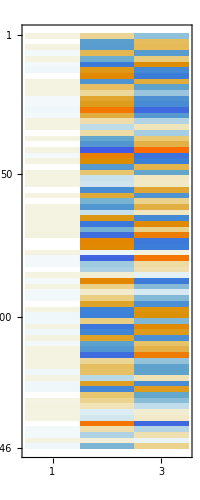

```mathematica
{m,k}={146,2};
d=RandomReal[{1,10},m];od=0.1 RandomReal[{-1,1},m-1];
B= SparseArray[{Band[{1,2}]->od,Band[{2,1}]->od,Band[{1,1}]->d},{m,m}];
A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
v0=RandomReal[{-1,1},m];
{V,HBig}=ArnoldiInitialize[A,B,v0,k];
(* Take some more steps *)
p=2;{V,HBig}=ArnoldiStep[A,B,{V,HBig},p];
(* run IRA filter *)
Q=IRAPurge[HBig,k,"LargeReal"];
(* Use Q to choose VPurge *)
VPurge=V⟦All,1;;k+p⟧.Q;
HPurge=Chop[Qᵀ.HBig⟦1;;k+p,1;;k+p⟧.Q];
Map[MatrixPlot,{A.VPurge⟦All,1;;-1⟧-(B.VPurge.HPurge)⟦All,1;;-1⟧}]
```

```mathematica
(* Check residuals and structure *)
TabView[{
"Init+Steps"->MatrixPlot[HBig,
PlotLabel->Map[Norm,
{Vᵀ.B.V-IdentityMatrix[k+p+1],
A.V⟦All,1;;k+p⟧-B.V.HBig}]],
"Purge"->MatrixPlot[HNew,
PlotLabel->Map[Norm,
{VPurgeᵀ.B.VPurge-IdentityMatrix[k+2],
A.VPurge⟦All,1;;k⟧}]]
}]
```

Thread::tdlen: Objects of unequal length in {{1.,2.80537×10^-17,1.39503×10^-16},{7.70461×10^-17,1.,«23»},{1.58844×10^-16,1.4962×10^-16,1.}}+{«1»} cannot be combined.

12

```mathematica
Map[Dimensions,{Q,HPurge}]
```

{{5,4},{4,3}}

```mathematica
A.VPurge⟦All,k⟧/(B.VPurge.HPurge)⟦All,k⟧
```

{11.6493,1.82396,1.79966,-0.392007,0.408416,2.52482,0.119927,-23.7993,0.970493,0.595668,-17.9966,7.20129,1.26912,0.740809}